Definicje funkcji używanych przy mapowaniu:

```mathematica
GetMax[x_] :={First[x], Max[Take[x,{2,Length[x]}]]};
GetMean[x_] :={First[x], Mean[Take[x,{2,Length[x]}]]};
GetVariance[x_] :={First[x], Variance[Take[x,{2,Length[x]}]]};
GetPlusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] + StandardDeviation[Take[x,{2,Length[x]}]]};
GetMinusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] - StandardDeviation[Take[x,{2,Length[x]}]]};
```

```mathematica
UNI :="uniform"; MIN := "minimum"; AGL := "always_go_left";
Strategies := {UNI, MIN, AGL};
CCP := "coupon_collector"; BPP := "birthday_paradox"; MLP := "max_load";
Problems := {CCP, BPP, MLP};
RawResults[s_,p_,d_] := ReadList[StringJoin["/home/dev/Workspaces/Studies/AnalAlgo/BallsAndCups/cups_" ,s,"_",p,"_",ToString[d],".m"], Number, RecordLists->True];
ResultsMax[s_,p_,d_] := Map[GetMax, RawResults[s,p,d]];
ResultsMean[s_,p_,d_] := Map[GetMean,  RawResults[s,p,d]];
ResultsVariance[s_,p_,d_] := Map[GetVariance,  RawResults[s,p,d]];
ResultsPlusStandardDeviation[s_,p_,d_] := Map[GetPlusStandardDeviation,  RawResults[s,p,d]];
ResultsMinusStandardDeviation[s_,p_,d_] := Map[GetMinusStandardDeviation,  RawResults[s,p,d]];
```

Wyświetlanie wyników dla Coupon Collector Problem z użyciem rozkładu jednostajnego:

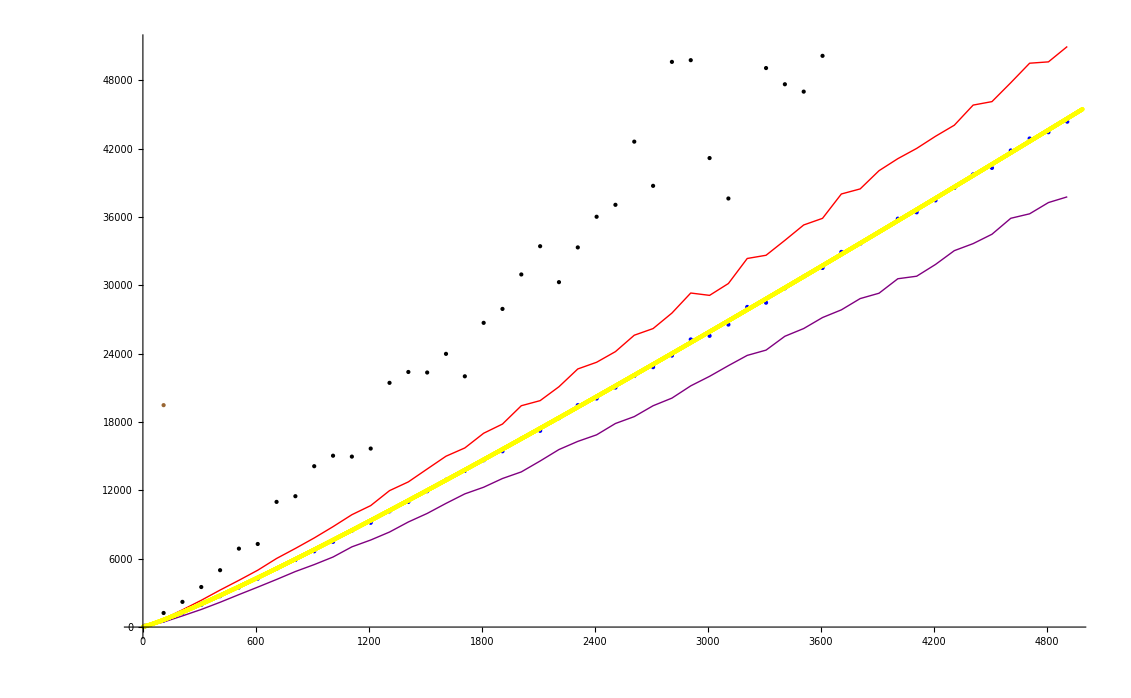

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[UNI,CCP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[UNI,CCP,10],PlotStyle->Purple],
ListPlot[ResultsMax[UNI,CCP,10],PlotStyle -> Black],
ListPlot[ResultsMean[UNI,CCP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[UNI,CCP,10], PlotStyle->Brown],
ListPlot[Table[n*HarmonicNumber[n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```

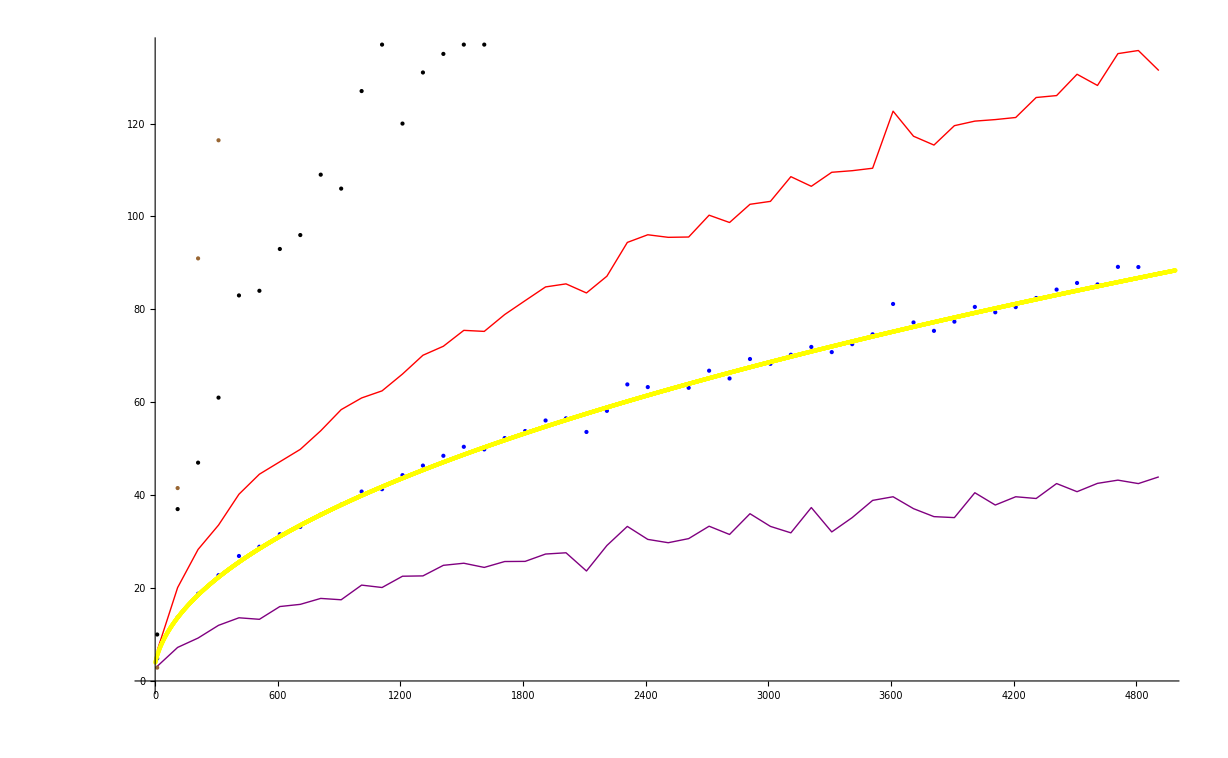

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[UNI,BPP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[UNI,BPP,10],PlotStyle->Purple],
ListPlot[ResultsMax[UNI,BPP,10],PlotStyle -> Black],
ListPlot[ResultsMean[UNI,BPP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[UNI,BPP,10], PlotStyle->Brown],
ListPlot[Table[1.25Sqrt[n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```

Wyświetlanie wyników dla Max Load Problem z użyciem rozkładu jednostajnego:

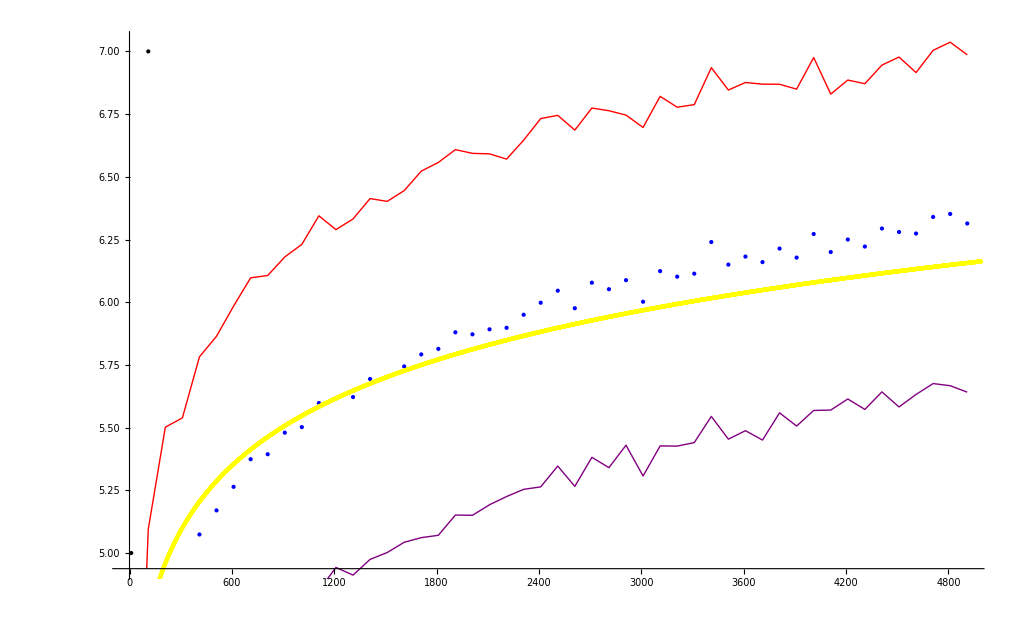

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[UNI,MLP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[UNI,MLP,10],PlotStyle->Purple],
ListPlot[ResultsMax[UNI,MLP,10],PlotStyle -> Black],
ListPlot[ResultsMean[UNI,MLP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[UNI,MLP,10], PlotStyle->Brown],
ListPlot[Table[1.55Log[n]/Log[Log[n]],{n, 10, 5000}], PlotStyle-> Yellow]
]
```